# cLTD

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

## Options

loopmom: (default: {k0,k1,k2,k3})
	defines the set of variable to be identified as loop momenta in the input expression

FORMpath: (default: form)
	defines the path to the binary “form”. By default it will assume that can be found in $PATH

tFORMpath: (default: tform)
	defines the path to the binary “tform”. By default it will assume that can be found in $PATH

WorkingDirectory: (default: NotebookDirecotry[])
	directory where to create the temporary FORM scripts.

FORM_ID: (default: None)
	The temporary FORM files are named cLTD_<FORM_ID>.frm and cLTD_<FORM_ID>.out
	By default this ID is made out of random letters, one can set it to something specific by setting this option.
	This is particularly useful together with keep_FORM_script->True.

FORMcores: (default: 1)
	Number of cores to use when running FORM. 
	When more than one core is selected then “tform” is used

keep_FORM_script: (default: False)
	Don’t eliminate the temporary files generated by the function call.

EvalAll: (default: False)
	Replace cLTDnorm and den in the output with their expressions.

NoNumerator: (default: False)
	When the expression has no numerator this option can be set to True.
	Avoiding the expensive generation of the numerator mappings will speed up the evaluation.

## Import cLTD

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD.m"];
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
FORMPATH="form";(*"<PASTE_HERE_YOUR_FULL_FORM_PATH_HERE_INSTEAD>"*)
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→./
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

## Examples

### Bubble

```mathematica
cBubble=cLTD[prop[k-p1,0]prop[k,0],"loopmom"->{k},"EvalAll"->True];
{cBubble[[1]],TableForm[cBubble[[2]]]}
```

{-(ⅈ (1/(E0+E1-p1[0])+1/(E0+E1+p1[0])))/(4 E0 E1),E0→√(k.k)
E1→√(k.k-2 k.p1+p1.p1)}

### One-Loop Photon Self Energy

```mathematica
(*One-loop photon self energy*)numerator=-4*SP4[k,p1]+4*m^2+8*SP4[pol,k]*SP4[cpol,k]+4*SP4[pol,p1]*SP4[cpol,k]+4*SP4[pol,k]*SP4[cpol,p1];
props=prop[k,m]*prop[k+p1,m];

(*Get the cLTD expression*)
cPhotonSelf=cLTD[numerator*props,loopmom->{k},"EvalAll"->True]
```

{-1/(4 E0 E1)ⅈ (8 cpol[0] k.pol+4 cpol[0] p1.pol+(4 m^2)/(E0+E1-p1[0])+(4 k.p1)/(E0+E1-p1[0])-(8 E1 cpol[0] k.pol)/(E0+E1-p1[0])+(8 cpol.k k.pol)/(E0+E1-p1[0])+(4 cpol.p1 k.pol)/(E0+E1-p1[0])-(4 E1 cpol[0] p1.pol)/(E0+E1-p1[0])+(4 cpol.k p1.pol)/(E0+E1-p1[0])+4 p1[0]-(4 E1 p1[0])/(E0+E1-p1[0])+(4 cpol[0] k.pol p1[0])/(E0+E1-p1[0])+(4 cpol[0] p1.pol p1[0])/(E0+E1-p1[0])+(4 p1[0]^2)/(E0+E1-p1[0])+(4 m^2)/(E0+E1+p1[0])+(4 k.p1)/(E0+E1+p1[0])-(8 E0 cpol[0] k.pol)/(E0+E1+p1[0])+(8 cpol.k k.pol)/(E0+E1+p1[0])+(4 cpol.p1 k.pol)/(E0+E1+p1[0])-(4 E0 cpol[0] p1.pol)/(E0+E1+p1[0])+(4 cpol.k p1.pol)/(E0+E1+p1[0])-(4 E0 p1[0])/(E0+E1+p1[0])-(4 cpol[0] k.pol p1[0])/(E0+E1+p1[0])-8 E0 cpol[0] pol[0]-8 E1 cpol[0] pol[0]+8 cpol.k pol[0]+4 cpol.p1 pol[0]+(8 E1^2 cpol[0] pol[0])/(E0+E1-p1[0])-(8 E1 cpol.k pol[0])/(E0+E1-p1[0])-(4 E1 cpol.p1 pol[0])/(E0+E1-p1[0])-(8 E1 cpol[0] p1[0] pol[0])/(E0+E1-p1[0])+(4 cpol.k p1[0] pol[0])/(E0+E1-p1[0])+(4 cpol.p1 p1[0] pol[0])/(E0+E1-p1[0])+(8 E0^2 cpol[0] pol[0])/(E0+E1+p1[0])-(8 E0 cpol.k pol[0])/(E0+E1+p1[0])-(4 E0 cpol.p1 pol[0])/(E0+E1+p1[0])+(8 E0 cpol[0] p1[0] pol[0])/(E0+E1+p1[0])-(4 cpol.k p1[0] pol[0])/(E0+E1+p1[0])),{E0→√(m^2+k.k),E1→√(m^2+k.k+2 k.p1+p1.p1)}}

```mathematica
numerator = SP4[p,k];
propagators = prop[k-p1,0]prop[k-w2,0];
cLTD[numerator * propagators ,"loopmom"->{k},"EvalAll"->True]
```

{-(ⅈ (-p[0]-(k.p)/(E0+E1+p1[0]-w2[0])+(E0 p[0])/(E0+E1+p1[0]-w2[0])+(p[0] p1[0])/(E0+E1+p1[0]-w2[0])-(k.p)/(E0+E1-p1[0]+w2[0])+(E1 p[0])/(E0+E1-p1[0]+w2[0])+(p[0] w2[0])/(E0+E1-p1[0]+w2[0])))/(4 E0 E1),{E0→√(k.k-2 k.p1+p1.p1),E1→√(k.k-2 k.w2+w2.w2)}}

### Decagon

```mathematica
Print["Total Time: ",Timing[cDecagon = cLTD[ prop[k-p1,0]prop[k-p2,0] prop[k-p3,0] prop[k-p4,0] prop[k-p5,0] prop[k-p6,0] prop[k-p7,0] prop[k-p8,0]prop[k-p9,0] prop[k-p10,0],
"loopmom"->{k},"EvalAll"->True];
][[1]]
];
Print["# terms:\t",Length[Expand[cDecagon[[1]]]]];
Print["Energies:\t",TableForm[cDecagon[[2]]]];
```

Total Time: 17.1185

# terms:	48620

Energies:	E0→√(k.k-2 k.p1+p1.p1)
E1→√(k.k-2 k.p10+p10.p10)
E2→√(k.k-2 k.p2+p2.p2)
E3→√(k.k-2 k.p3+p3.p3)
E4→√(k.k-2 k.p4+p4.p4)
E5→√(k.k-2 k.p5+p5.p5)
E6→√(k.k-2 k.p6+p6.p6)
E7→√(k.k-2 k.p7+p7.p7)
E8→√(k.k-2 k.p8+p8.p8)
E9→√(k.k-2 k.p9+p9.p9)

### Double Box

```mathematica
(*Doube box*)expr=prop[k,0]*prop[k-p1,0]*prop[k+p2,0]*prop[k-l,0]*prop[l+p2,0]*prop[l+p2+p3,0]*prop[l-p1,0];

(*Get the cLTD expression*)
Print["Total Time: ",Timing[
cDoubleBox=cLTD[expr,loopmom->{k,l}];
][[1]]
];

Print["# terms:\t",Length[Expand[cDoubleBox[[1]]]]];
Print["Energies:\t",TableForm[cDoubleBox[[2]]]];
```

Total Time: 0.427601

# terms:	252

Energies:	E0→√(k.k)
E1→√(k.k-2 k.l+l.l)
E2→√(k.k-2 k.p1+p1.p1)
E3→√(l.l-2 l.p1+p1.p1)
E4→√(k.k+2 k.p2+p2.p2)
E5→√(l.l+2 l.p2+p2.p2)
E6→√(l.l+2 l.p2+2 l.p3+p2.p2+2 p2.p3+p3.p3)

## Evaluation

```mathematica
(*As example we consider the 2x2 Fishnet topology*)
loopmomenta={l1,l2,l3,l4};
propagators={l1,l1-p[1],l1+l2+p[7]+p[9],l2-p[3],l2,l1-l3,l3,l2-l4,l3+l4+p[7]+p[9],l4,l3+p[7],l4+p[9]};
expr=Times@@Map[prop[#,0]&,propagators]
```

prop[l1,0] prop[l2,0] prop[l1-l3,0] prop[l3,0] prop[l2-l4,0] prop[l4,0] prop[l1-p[1],0] prop[l2-p[3],0] prop[l3+p[7],0] prop[l4+p[9],0] prop[l1+l2+p[7]+p[9],0] prop[l3+l4+p[7]+p[9],0]

```mathematica
(*Obtain the cLTD expression*)
{cLTDexpr, EnergySubs}=cLTD[expr,"loopmom"->loopmomenta,"NoNumerator"->True];
```

### Collect by Denominators

```mathematica
ClearAll[cLTDfastHornerForm]
cLTDfastHornerForm[expr_]:=cLTDfastHornerForm[expr]=Module[{
newexpr=expr/.cLTDnorm->den,
densub,exprdens},
densub = Module[{ii=0},
Table[ToExpression["den"<>ToString[ii++]]->denominator,{denominator,Cases[newexpr,_den,Infinity]//Union}]
];
exprdens = newexpr/.Reverse/@densub;
densub =SortBy[densub,Count[exprdens,#[[1]],Infinity]&];
exprdens=Collect[exprdens,First/@densub];
{exprdens, densub}
]
```

```mathematica
(* We evaluate each unique denominator only once and then replace 
that value into the cLTD expression *)
FastEvaluatePrepare[expr_]:=Module[{},cLTDfastHornerForm[expr]; ];
FastEvaluate[expr_, energysubs_,numsubs_]:=Module[{densub, exprdens},
{exprdens,densub}=cLTDfastHornerForm[expr];
Block[Evaluate[First/@densub],(densub/.den[a_]:>1/a/.Join[numsubs,energysubs/.numsubs])/.Rule->Set;
exprdens/.Join[numsubs,energysubs/.numsubs]]
]
```

### Evaluate

```mathematica
(*Random evalution point*)
SeedRandom[1];
numeval16=Table[{
var[0]->SetPrecision[RandomReal[{-1,1}],16],
var->SetPrecision[RandomReal[{-1,1},3],16]}
,{var,Variables[propagators]}]/.Rule[(Alternatives@@LoopMom)[0],_]:>Nothing//Flatten
```

{l1[0]→0.6347789803421424,l1→{-0.7771607777375271,0.5790519892677031,-0.6243937065879472},l2[0]→-0.5172780650846991,l2→{-0.8685224809824379,0.08449324101924827,-0.5376909865279451},l3[0]→-0.2079878369028259,l3→{0.4009475638844897,-0.576348041891745,0.4973137629658959},l4[0]→-0.1542987013201023,l4→{-0.505010438271984,0.9543435234815529,0.6503258789770276},p[1][0]→0.8505504023577255,p[1]→{0.1561123039887584,-0.414260526404155,-0.5838978704388147},p[3][0]→0.1609489625883174,p[3]→{-0.7423583307231256,-0.3871452399307636,0.4240241401515581},p[7][0]→-0.2188362572398517,p[7]→{0.6399344735703592,-0.3492970040094185,0.1865204550155899},p[9][0]→0.03754833408032709,p[9]→{-0.661973966244501,-0.05486971360712189,0.6143216038144992}}

```mathematica
(*Cache Horner Form*)
FastEvaluatePrepare[cLTDexpr]
```

```mathematica
(*Evaluate*)
FastEvaluate[cLTDexpr,EnergySubs,numeval16]//AbsoluteTiming
```

{0.038241,1.0290928956631×10^-6}

### Precision Plot

```mathematica
(*Rescale l1 -> λ l1*)
numeval16λ = numeval16/.Rule[l1,v_]:>Rule[l1,λ v];
(*Eval points for logλ ϵ [-10,10]*)
numeval16λpoints=Table[{logλ,numeval16λ/.{λ->Exp[logλ]}},{logλ,-10,10,1/10}];
```

```mathematica
(* Get the precision of the expression after evaluation (INPUT precision 16 digits) *)
cltdλ=Table[{point[[1]],FastEvaluate[cLTDexpr,EnergySubs,point[[2]]]},{point, numeval16λpoints}];//AbsoluteTiming
cltdλPrecision=Table[{point[[1]],Precision[point[[2]]]},{point, cltdλ}];
```

{7.86639,Null}

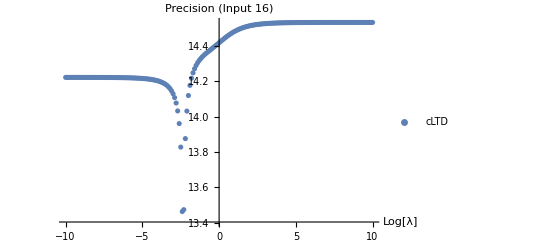

```mathematica
(*Plot to show that the precision is stable in the whole range.
The dip is an artefact of the expression going to zero. *)
ListPlot[{cltdλPrecision},
PlotLegends->{"cLTD"},
AxesLabel->{"Log[λ]","Precision (Input 16)"}]
```

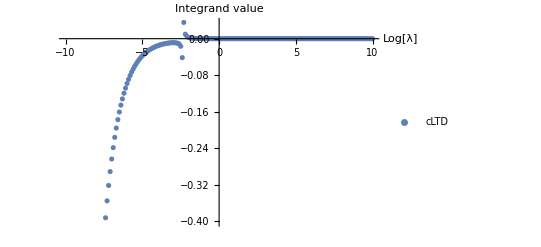

```mathematica
(*The dip is an artefact of the expression going to zero. *)
ListPlot[{cltdλ},
PlotLegends->{"cLTD"},
AxesLabel->{"Log[λ]","Integrand value"}]
```

## Cross-free Family generation and LTD from graphs

### Box1L

#### no external, no masses

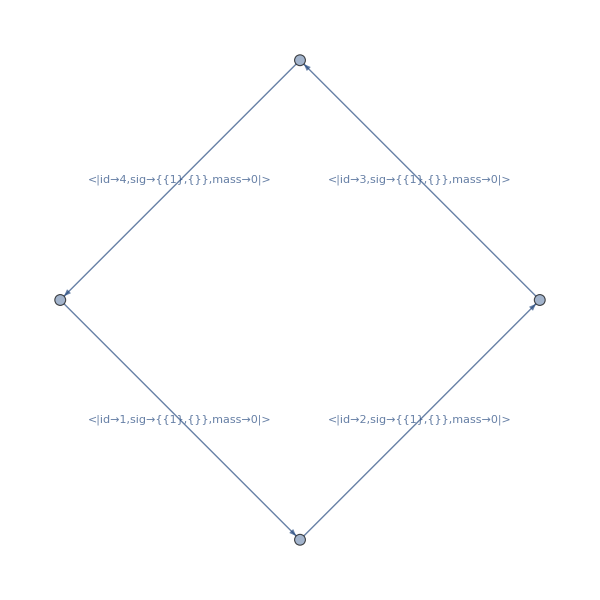

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=DirectedGraph[AssignSignatures[Box1L,masses-><|3->0|>,lmb->{1}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7}}

```mathematica
Box1LcLTDexpr=GeneratecLTDExpression[Box1L,FORMpath->FORMPATH]
```

{(5 ⅈ)/(32 E0^7),{E0→√(k1.k1)}}

```mathematica
EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]
```

(703550211328125 ⅈ)/(97434946105088 √14494)

```mathematica
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
```

Or see the factorised human-readable expression as follows:

```mathematica
CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->False]//MatrixForm
```

({True,True,True,False} | 1/((OSE[1]+OSE[4]) (OSE[2]+OSE[4]) (OSE[3]+OSE[4]))
{True,True,False,True} | 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]) (OSE[3]+OSE[4]))
{True,True,False,False} | (1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]))+1/((OSE[2]+OSE[3]) (OSE[2]+OSE[4])))/(OSE[1]+OSE[4])
{True,False,True,True} | 1/((OSE[1]+OSE[2]) (OSE[2]+OSE[3]) (OSE[2]+OSE[4]))
{True,False,True,False} | (1/((OSE[1]+OSE[2]) (OSE[2]+OSE[3]))+1/((OSE[2]+OSE[3]) (OSE[3]+OSE[4])))/(OSE[1]+OSE[4])
{True,False,False,True} | (1/((OSE[1]+OSE[2]) (OSE[1]+OSE[3]))+1/((OSE[1]+OSE[2]) (OSE[2]+OSE[4])))/(OSE[3]+OSE[4])
{True,False,False,False} | 1/((OSE[1]+OSE[2]) (OSE[1]+OSE[3]) (OSE[1]+OSE[4]))
{False,True,True,True} | 1/((OSE[1]+OSE[2]) (OSE[1]+OSE[3]) (OSE[1]+OSE[4]))
{False,True,True,False} | (1/((OSE[1]+OSE[3]) (OSE[3]+OSE[4]))+1/((OSE[2]+OSE[4]) (OSE[3]+OSE[4])))/(OSE[1]+OSE[2])
{False,True,False,True} | (1/((OSE[2]+OSE[3]) (OSE[3]+OSE[4]))+1/((OSE[1]+OSE[4]) (OSE[3]+OSE[4])))/(OSE[1]+OSE[2])
{False,True,False,False} | 1/((OSE[1]+OSE[2]) (OSE[2]+OSE[3]) (OSE[2]+OSE[4]))
{False,False,True,True} | (1/((OSE[1]+OSE[3]) (OSE[1]+OSE[4]))+1/((OSE[1]+OSE[4]) (OSE[2]+OSE[4])))/(OSE[2]+OSE[3])
{False,False,True,False} | 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]) (OSE[3]+OSE[4]))
{False,False,False,True} | 1/((OSE[1]+OSE[4]) (OSE[2]+OSE[4]) (OSE[3]+OSE[4])))

```mathematica
EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics]
```

(703550211328125 ⅈ)/(97434946105088 √14494)

#### no external, with masses

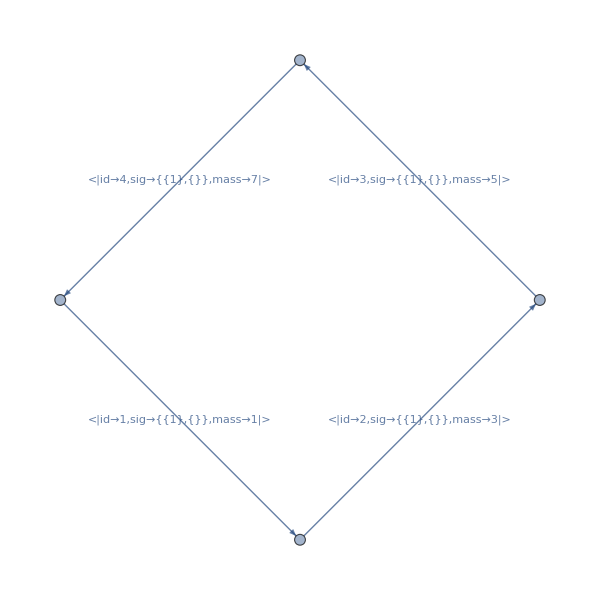

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=DirectedGraph[AssignSignatures[Box1L,masses-><|1->1,2->3,3->5,4->7|>,lmb->{1}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7}}

```mathematica
Box1LcLTDexpr=GeneratecLTDExpression[Box1L];
```

```mathematica
EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,0.0000142998]

```mathematica
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,0.0000142998]

#### with external, with masses

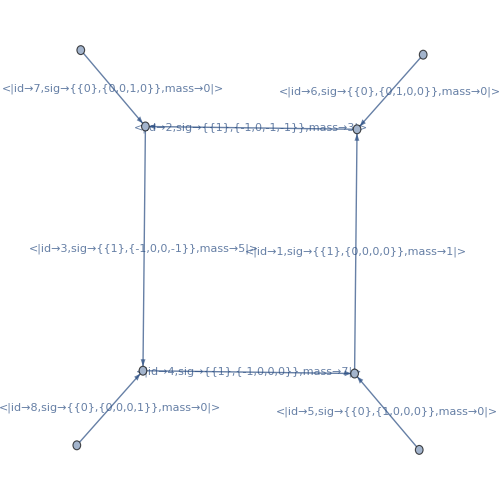

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[3,4,3],DirectedEdge[4,1,4],
DirectedEdge[101,1,5],DirectedEdge[102,2,6],DirectedEdge[103,3,7],DirectedEdge[104,4,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=DirectedGraph[AssignSignatures[Box1L,masses-><|1->1,2->3,3->5,4->7|>,lmb->{1}],EdgeLabels->Automatic,ImageSize->500,GraphLayout->"HighDimensionalEmbedding"]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p3→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3E→47/53,p4→{-15981/6479,-27769/11063,-49729/20213},p4E→-295115/107113}

```mathematica
Box1LcLTDexpr=GeneratecLTDExpression[Box1L];
```

```mathematica
EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,7.18014×10^-6]

```mathematica
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics]//N//FullForm
```

Complex[0.,7.18014×10^-6]

#### with external, with masses, with numerator

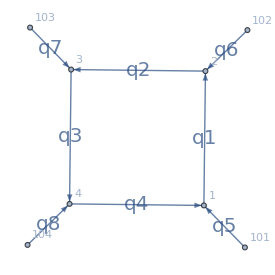

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],DirectedEdge[3,4,3],DirectedEdge[4,1,4],
DirectedEdge[101,1,5],DirectedEdge[102,2,6],DirectedEdge[103,3,7],DirectedEdge[104,4,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=AssignSignatures[Box1L,masses-><|1->1,2->2,3->3,4->4|>,lmb->{1}];
Box1L=DirectedGraph[Box1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Box1L]}]]
```

```mathematica
Box1Lnumerics=GenerateRandomSample[Box1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p3→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3E→47/53,p4→{-15981/6479,-27769/11063,-49729/20213},p4E→-295115/107113}

Note that q[1] = q[4] + q[5] !

```mathematica
Print["Note that q[1] = q[4] + q[5]"];
Print[""];
Box1Lnumerator=SP4[q[1],q[1]] ;
Print["Numerator considered: ",Box1Lnumerator]
Box1LcLTDexpr=GeneratecLTDExpression[Box1L,Num->Box1Lnumerator];
Print["cLTD result: ",EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm];
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics,Num->Box1Lnumerator,DEBUG->False]//N//FullForm];
Print[""];
Box1Lnumerator=SP4[q[1],q[4]+q[5]];
Print["Numerator considered: ",Box1Lnumerator]
Box1LcLTDexpr=GeneratecLTDExpression[Box1L,Num->Box1Lnumerator];
Print["cLTD result: ",EvalcLTD[Box1LcLTDexpr,Box1Lnumerics]//N//FullForm];
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics,Num->Box1Lnumerator,DEBUG->False]//N//FullForm];
Print[""];
```

Note that q[1] = q[4] + q[5]

Numerator considered: SP4[q[1],q[1]]

cLTD result: Complex[0.,-0.000140916]

cFF result : 0.

Numerator considered: SP4[q[1],q[4]+q[5]]

cLTD result: Complex[0.,-0.000140916]

cFF result : Complex[0.,-0.000140916]

Notice an alternative formulation of the numerator with an explicit expression of the energy and spatial part of the edge momentum

```mathematica
Box1Lnumerator=qE[1]*qE[4]+q[1][0]*q[5][0]-q[1].q[4]-q[1].q[5];
Box1LcFFexpr=CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True];
Print["cFF result : ",EvalcFF[Box1L,Box1LcFFexpr,Box1Lnumerics,Num->Box1Lnumerator,DEBUG->False]//N//FullForm];
Print[""];
```

cFF result : Complex[0.,-0.000140916]

### Banana2L

#### no external, no masses

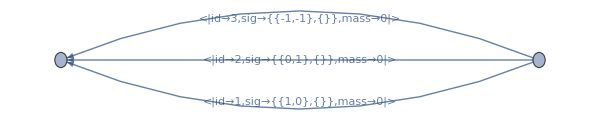

```mathematica
Banana2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[1,2,2],
DirectedEdge[1,2,3]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Banana2L=DirectedGraph[AssignSignatures[Banana2L,masses-><|3->0|>,lmb->{1,2}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
Banana2Lnumerics=GenerateRandomSample[Banana2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
Banana2LcLTDexpr=GeneratecLTDExpression[Banana2L];
```

```mathematica
EvalcLTD[Banana2LcLTDexpr,Banana2Lnumerics]//N//FullForm
```

0.0139442

```mathematica
Banana2LcFFexpr=CrossFreeFamilyLTD[Banana2L,ConvertToNormalisedFormat->True]
```

{<|Orientation→{-1,-1,-1},Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,3},shift_signature→{}|>}|>}|>,<|Orientation→{1,1,1},Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,3},shift_signature→{}|>}|>}|>}

```mathematica
EvalcFF[Banana2L,Banana2LcFFexpr,Banana2Lnumerics]//N//FullForm
```

0.0139442

### DottedBanana2L

#### no external, with masses

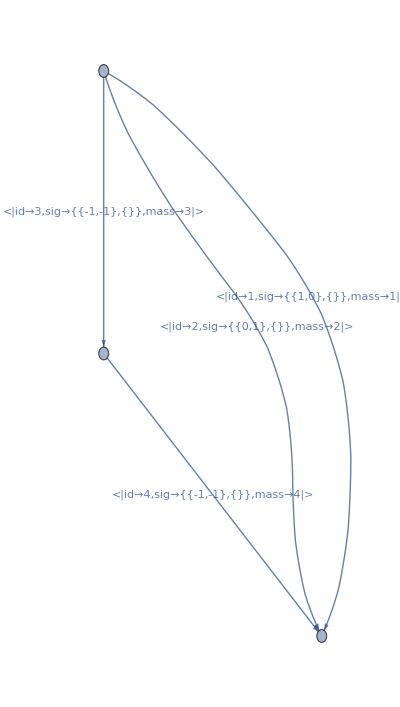

```mathematica
myGraph=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[1,2,2],
DirectedEdge[1,3,3],DirectedEdge[3,2,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
myGraph=DirectedGraph[AssignSignatures[myGraph,masses->Association[Table[i->i,{i,Range[4]}]],lmb->{1,2}],EdgeLabels->Automatic,ImageSize->400]
```

```mathematica
myGraphcLTDexpr=GeneratecLTDExpression[myGraph]
```

{-(2/((E1+E2) (E0+E1+E3))+2/((E1+E2) (E0+E2+E3))+2/((E0+E1+E3) (E0+E2+E3)))/(16 E0 E1 E2 E3),{E0→√(1+k1.k1),E1→√(9+k1.k1+2 k1.k2+k2.k2),E2→√(16+k1.k1+2 k1.k2+k2.k2),E3→√(4+k2.k2)}}

```mathematica
myGraphnumerics=GenerateRandomSample[myGraph,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
myGraphcLTDexpr=GeneratecLTDExpression[myGraph];
```

```mathematica
EvalcLTD[myGraphcLTDexpr,myGraphnumerics]//N//FullForm
```

-0.0000825856

```mathematica
myGraphcFFexpr=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[myGraph,myGraphcFFexpr,myGraphnumerics]//N//FullForm
```

-0.0000825856

Now considering orientation: {-1, -1, 1, -1}

------------------------------------------------------------

Now considering the following graph:

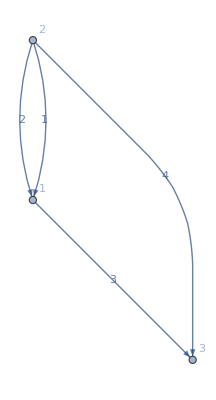

Found the following sources (first one will be considered): {2}

Edges to be contracted (possibly won't contribute all): {1,2,4}

Contributing edge contractions: {21<|id→1,sig→{{1,0},{}},mass→1|>}

Esurf for this term: {1,2,4}

------------------------------------------------------------

Now considering the following graph:

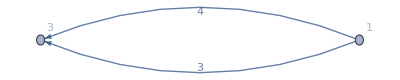

Reached termination condition, returning Esurf:{3,4}

Complete term returned at this level: 1/((OSE[1]+OSE[2]+OSE[4]) (OSE[3]+OSE[4]))

------------------------------------------------------------

{{{True,True,False,True},1/((OSE[1]+OSE[2]+OSE[4]) (OSE[3]+OSE[4]))}}

```mathematica
CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->False,
Orientations->{Table[o===-1,{o,myGraphcFFexpr⟦3⟧["Orientation"]}]},
DEBUG->True]
```

### DoubleTriangle2L

#### no external, no masses

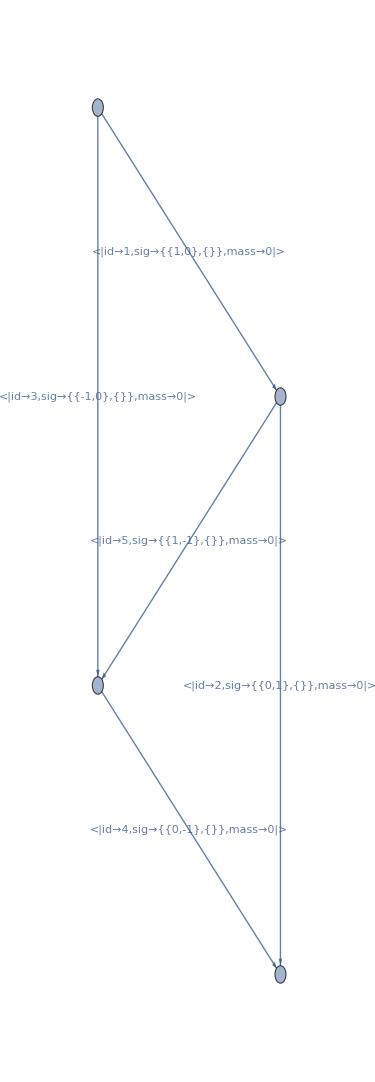

```mathematica
DoubleTriangle2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[1,4,3],DirectedEdge[4,3,4],
DirectedEdge[2,4,5]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleTriangle2L=DirectedGraph[AssignSignatures[DoubleTriangle2L,masses-><||>,lmb->{1,2}],EdgeLabels->Automatic,ImageSize->375]
```

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L]
```

{-(-4/(E0+E2+E3)^3-2/(E0 (E0+E2+E3)^2)-2/(E3 (E0+E2+E3)^2)-2/(E0 E3 (E0+E2+E3)))/(32 E0^2 E2 E3^2),{E0→√(k1.k1),E1→√(k1.k1),E2→√(k1.k1-2 k1.k2+k2.k2),E3→√(k2.k2),E4→√(k2.k2)}}

```mathematica
DoubleTriangle2Lnumerics=GenerateRandomSample[DoubleTriangle2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L];
```

```mathematica
EvalcLTD[DoubleTriangle2LcLTDexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

0.0629388

```mathematica
DoubleTriangle2LcFFexpr=CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleTriangle2L,DoubleTriangle2LcFFexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

0.0629388

Now considering orientation: {-1, -1, -1, -1, -1}

------------------------------------------------------------

Now considering the following graph:

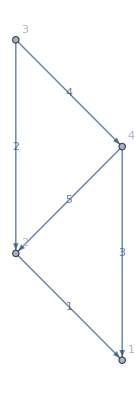

Found the following sources and sinks(first eligible one will be considered):
source {3}
sinks {1}

Edges to be contracted (possibly won't contribute all): {2,4}

Contributing edge contractions: {34<|id→4,sig→{{0,-1},{}},mass→0|>}

Esurf for this term: {1,{2,4}}

------------------------------------------------------------

Now considering the following graph:

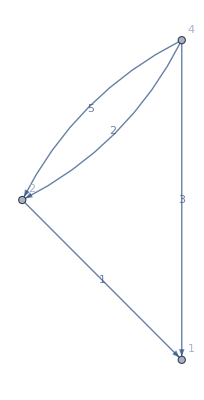

Found the following sources and sinks(first eligible one will be considered):
source {4}
sinks {1}

Edges to be contracted (possibly won't contribute all): {3,2,5}

Contributing edge contractions: {42<|id→2,sig→{{0,1},{}},mass→0|>}

Esurf for this term: {1,{3,2,5}}

------------------------------------------------------------

Now considering the following graph:

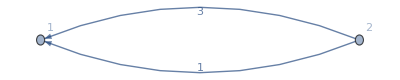

Reached termination condition, returning Esurf:{1,3}

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

{{{True,True,True,True,True},1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))}}

```mathematica
CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->False,
Orientations->{Table[o===-1,{o,DoubleTriangle2LcFFexpr⟦1⟧["Orientation"]}]},
DEBUG->True]
```

#### with external, no masses

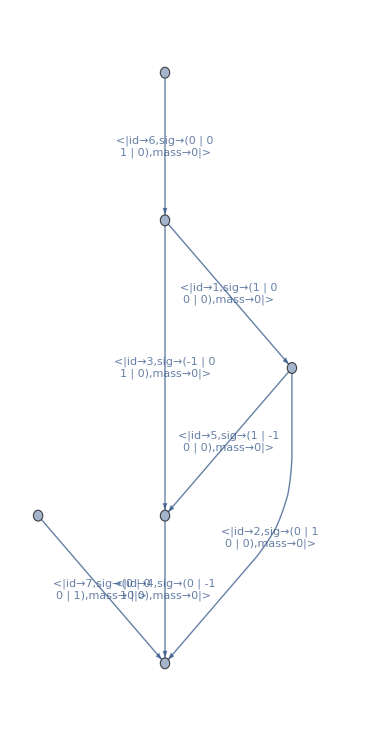

```mathematica
DoubleTriangle2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[1,4,3],DirectedEdge[4,3,4],
DirectedEdge[2,4,5],
DirectedEdge[101,1,6],DirectedEdge[102,3,7]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleTriangle2L=DirectedGraph[AssignSignatures[DoubleTriangle2L,masses-><||>,lmb->{1,2}],EdgeLabels->Automatic,ImageSize->375]
```

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L]
```

{-1/(32 E0 E1 E2 E3 E4)(-1/((E0+E1+E2) (E1+E3+E4) (E1+E2+E3-p1E))-1/((E1+E3+E4) (E0+E3-p1E) (E1+E2+E3-p1E))-1/((E0+E1+E2) (E1+E3+E4) (E0+E1+E4-p1E))-1/((E0+E1+E2) (E0+E3-p1E) (E0+E1+E4-p1E))-1/((E0+E1+E2) (E1+E2+E3-p1E) (E2+E4-p1E))-1/((E0+E3-p1E) (E1+E2+E3-p1E) (E2+E4-p1E))-1/((E1+E3+E4) (E0+E1+E4-p1E) (E2+E4-p1E))-1/((E0+E3-p1E) (E0+E1+E4-p1E) (E2+E4-p1E))-1/((E0+E1+E2) (E2+E4-p1E) (E0+E3+p1E))-1/((E1+E3+E4) (E2+E4-p1E) (E0+E3+p1E))-1/((E0+E1+E2) (E1+E3+E4) (E1+E2+E3+p1E))-1/((E1+E3+E4) (E0+E3+p1E) (E1+E2+E3+p1E))-1/((E0+E1+E2) (E1+E3+E4) (E0+E1+E4+p1E))-1/((E0+E1+E2) (E0+E3+p1E) (E0+E1+E4+p1E))-1/((E0+E1+E2) (E0+E3-p1E) (E2+E4+p1E))-1/((E1+E3+E4) (E0+E3-p1E) (E2+E4+p1E))-1/((E0+E1+E2) (E1+E2+E3+p1E) (E2+E4+p1E))-1/((E0+E3+p1E) (E1+E2+E3+p1E) (E2+E4+p1E))-1/((E1+E3+E4) (E0+E1+E4+p1E) (E2+E4+p1E))-1/((E0+E3+p1E) (E0+E1+E4+p1E) (E2+E4+p1E))),{E0→√(k1.k1),E1→√(k1.k1-2 k1.k2+k2.k2),E2→√(k2.k2),E3→√(k1.k1-2 k1.p1+p1.p1),E4→√(k2.k2-2 k2.p1+p1.p1)}}

```mathematica
DoubleTriangle2Lnumerics=GenerateRandomSample[DoubleTriangle2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p1E→29/31,p2→{-17/19,-19/23,-23/29},p2E→-29/31}

```mathematica
DoubleTriangle2LcLTDexpr=GeneratecLTDExpression[DoubleTriangle2L];
```

```mathematica
EvalcLTD[DoubleTriangle2LcLTDexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

16.9042

```mathematica
DoubleTriangle2LcFFexpr=CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleTriangle2L,DoubleTriangle2LcFFexpr,DoubleTriangle2Lnumerics]//N//FullForm
```

16.9042

```mathematica
CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->True]
```

{<|Orientation→<|1→-1,3→-1,2→-1,5→-1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→-1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→-1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→-1,2→1,5→1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,3,2,4},shift_signature→{0,0}|>,<|OSE→{1,3},shift_signature→{1,0}|>}|>}|>,<|Orientation→<|1→-1,3→1,2→-1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→-1,3→1,2→1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→-1,3→1,2→1,5→1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,2,5},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>,<|Orientation→<|1→1,3→-1,2→-1,5→-1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→-1,2→-1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>,<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{3,2,5},shift_signature→{1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→-1,2→1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{3,5,4},shift_signature→{0,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→-1,5→-1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→-1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{1,2,5},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→-1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→1,5→-1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{1,5,4},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→1,5→1,4→-1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{3,5,4},shift_signature→{0,0}|>}|>}|>,<|Orientation→<|1→1,3→1,2→1,5→1,4→1|>,Terms→{<|Num→1,Orderings→Null,Esurfs→{<|OSE→{1,3},shift_signature→{-1,0}|>,<|OSE→{3,2,5},shift_signature→{-1,0}|>,<|OSE→{2,4},shift_signature→{-1,0}|>}|>}|>}

```mathematica
CrossFreeFamilyLTD[DoubleTriangle2L,ConvertToNormalisedFormat->False,
Orientations->{Table[o===-1,{o,DoubleTriangle2LcFFexpr⟦1⟧["Orientation"]}]},
DEBUG->True]
```

Now considering orientation: {-1, -1, -1, -1, -1}

------------------------------------------------------------

Now considering the following graph:

-Graphics-

Found the following sources (first one will be considered): {3}

Edges to be contracted (possibly won't contribute all): {2,4}

Contributing edge contractions: {34<|id→4,sig→{{0,-1},{1,0}},mass→0|>}

Esurf for this term: {2,4}

------------------------------------------------------------

Now considering the following graph:

-Graphics-

Found the following sources (first one will be considered): {4}

Edges to be contracted (possibly won't contribute all): {3,2,5}

Contributing edge contractions: {42<|id→2,sig→{{0,1},{0,0}},mass→0|>}

Esurf for this term: {3,2,5}

------------------------------------------------------------

Now considering the following graph:

-Graphics-

Reached termination condition, returning Esurf:{1,3}

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

Complete term returned at this level: 1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))

------------------------------------------------------------

{{{True,True,True,True,True},1/((OSE[1]+OSE[3]) (OSE[2]+OSE[4]) (OSE[2]+OSE[3]+OSE[5]))}}

### DoubleBox2L

#### no external, with masses

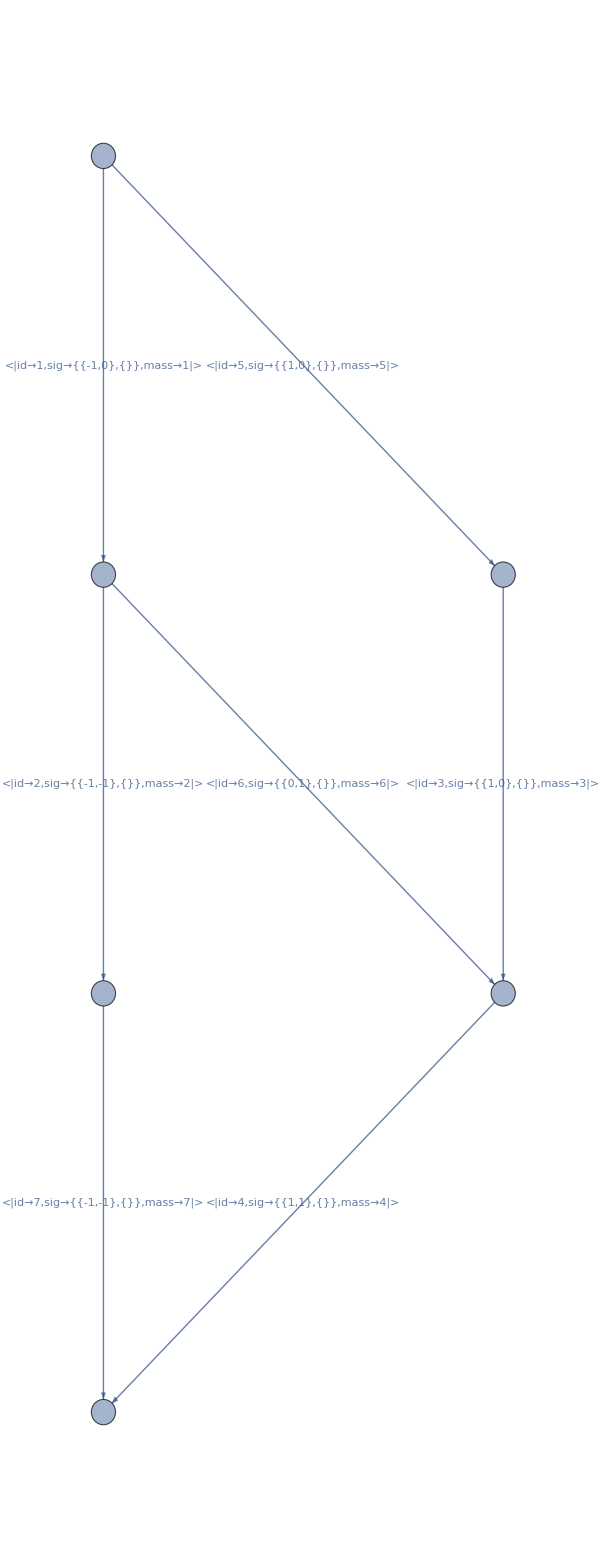

```mathematica
DoubleBox2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[1,4,5],DirectedEdge[2,5,6],DirectedEdge[3,6,7]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleBox2L=DirectedGraph[AssignSignatures[DoubleBox2L,
masses->Association[Table[i->i,{i,Range[7]}]],
lmb->{5,6}],EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
DoubleBox2Lnumerics=GenerateRandomSample[DoubleBox2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17}}

```mathematica
DoubleBox2LcLTDexpr=GeneratecLTDExpression[DoubleBox2L];
```

```mathematica
EvalcLTD[DoubleBox2LcLTDexpr,DoubleBox2Lnumerics]//N//FullForm
```

1.17694×10^-9

```mathematica
DoubleBox2LcFFexpr=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleBox2L,DoubleBox2LcFFexpr,DoubleBox2Lnumerics]//N//FullForm
```

1.17694×10^-9

#### with masses, with externals

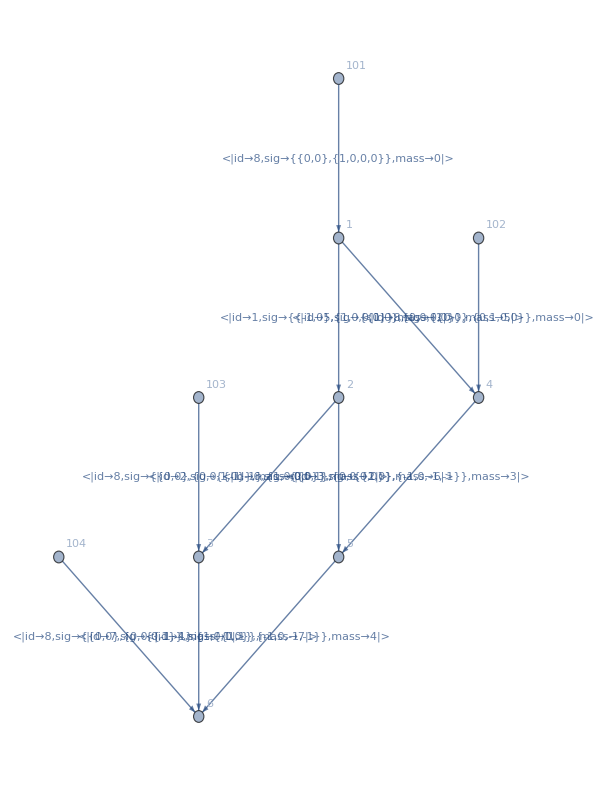

```mathematica
DoubleBox2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[1,4,5],DirectedEdge[2,5,6],DirectedEdge[3,6,7],
DirectedEdge[101,1,8],DirectedEdge[102,4,8],DirectedEdge[103,3,8],DirectedEdge[104,6,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleBox2L=DirectedGraph[AssignSignatures[DoubleBox2L,
masses->Association[Table[i->i,{i,Range[7]}]],
lmb->{5,6}],VertexLabels->Automatic,EdgeLabels->Automatic,ImageSize->600]
```

```mathematica
DoubleBox2Lnumerics=GenerateRandomSample[DoubleBox2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p3→{41/43,43/47,47/53},p1E→53/59,p2E→59/61,p3E→61/67,p4→{-70503/25327,-103145/39997,-162731/63017},p4E→-669377/241133}

```mathematica
DoubleBox2LcLTDexpr=GeneratecLTDExpression[DoubleBox2L];
```

```mathematica
EvalcLTD[DoubleBox2LcLTDexpr,DoubleBox2Lnumerics]//N//FullForm
```

2.22237×10^-9

```mathematica
DoubleBox2LcFFexpr=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleBox2L,DoubleBox2LcFFexpr,DoubleBox2Lnumerics]//N//FullForm
```

2.22237×10^-9

#### with masses, with externals, with numerator

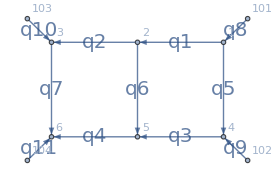

```mathematica
DoubleBox2L=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[1,4,5],DirectedEdge[2,5,6],DirectedEdge[3,6,7],
DirectedEdge[101,1,8],DirectedEdge[102,4,9],DirectedEdge[103,3,10],DirectedEdge[104,6,11]
},VertexLabels->Automatic,EdgeLabels->Automatic];
DoubleBox2L=DirectedGraph[AssignSignatures[DoubleBox2L,
masses->Association[Table[i->i,{i,Range[7]}]],
lmb->{5,6}]];
DirectedGraph[DoubleBox2L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[DoubleBox2L]}]]
```

```mathematica
DoubleBox2Lnumerics=GenerateRandomSample[DoubleBox2L,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p3→{41/43,43/47,47/53},p1E→53/59,p2E→59/61,p3E→61/67,p4→{-70503/25327,-103145/39997,-162731/63017},p4E→-669377/241133}

```mathematica
DoubleBox2LNumerator=SP4[q[2],q[7]]+SP4[q[4],q[6]]+SP4[q[3],q[5]]+SP4[q[1],q[8]]
```

SP4[q[1],q[8]]+SP4[q[2],q[7]]+SP4[q[3],q[5]]+SP4[q[4],q[6]]

```mathematica
DoubleBox2LcLTDexpr=GeneratecLTDExpression[DoubleBox2L,Num->DoubleBox2LNumerator];
```

```mathematica
EvalcLTD[DoubleBox2LcLTDexpr,DoubleBox2Lnumerics]//N//FullForm
```

-3.48404×10^-8

```mathematica
DoubleBox2LcFFexpr=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[DoubleBox2L,DoubleBox2LcFFexpr,DoubleBox2Lnumerics,Num->DoubleBox2LNumerator]//N//FullForm
```

-3.48404×10^-8

```mathematica
DoubleBox2LcFFexprFactorised=CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->False];
CompareOPCount[DoubleBox2LcLTDexpr,DoubleBox2LcFFexprFactorised]
```

CompareOPCount[{-(-2/((E0+E2+p1E) (E3+E4+p3E) (E0+E1+E4+p1E+p3E))-3/((E1+E5+E6) (E1+E2+E4+p3E) (E1+E4+E5-p4E))+18526+(p1.p3)/((E2+E5+p3E+p4E) (E1+E3+E5+p3E+p4E) (E3+E6+p3E+p4E) (E2+E3+E4+E5+2 p3E+p4E) (E0+E3+E4+E5+p1E+2 p3E+p4E)))/(128 E0 E1 E2 E3 E4 E5 E6),{E0→√(25+k1.k1),E1→√(36+k2.k2),E2→√(1+k1.k1-2 k1.p1+p1.p1),E3→√(4+k1.k1+6+p1.p1),E4→√(49+k1.k1+10+p1.p1+2 p1.p3+p3.p3),E5→√(9+k1.k1-2 k1.p1-2 k1.p3-2 k1.p4+p1.p1+2 p1.p3+2 p1.p4+p3.p3+2 p3.p4+p4.p4),E6→√(16+k1.k1+2 k1.k2-2 k1.p1-2 k1.p3-2 k1.p4+k2.k2-2 k2.p1-2 k2.p3-2 k2.p4+p1.p1+2 p1.p3+2 p1.p4+p3.p3+2 p3.p4+p4.p4)}},{1}]
 |  |  |  |

```mathematica
CrossFreeFamilyLTD[DoubleBox2L,ConvertToNormalisedFormat->False,Orientations->{DoubleBox2LcFFexprFactorised⟦1⟧⟦1⟧},DEBUG->False]
```

{{{True,True,True,True,True,True,True},((1/((OSE[2]+OSE[4]) (OSE[4]+OSE[7]))+1/((OSE[4]+OSE[7]) (OSE[3]+OSE[6]+OSE[7])))/((OSE[1]+OSE[3]) (OSE[2]+OSE[3]+OSE[6]))+(1/((OSE[4]+OSE[7]) (OSE[3]+OSE[6]+OSE[7]) (OSE[5]+OSE[6]+OSE[7]))+(1/((OSE[2]+OSE[4]) (OSE[4]+OSE[7]))+1/((OSE[4]+OSE[7]) (OSE[3]+OSE[6]+OSE[7])))/(OSE[2]+OSE[3]+OSE[6]))/(OSE[2]+OSE[5]+OSE[6]))/(OSE[1]+OSE[5])}}

### 2x2 Fishnet

#### with external, with masses

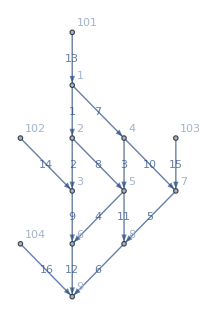

```mathematica
myGraph=DirectedGraph[{
DirectedEdge[1,2,1],DirectedEdge[2,3,2],
DirectedEdge[4,5,3],DirectedEdge[5,6,4],
DirectedEdge[7,8,5],DirectedEdge[8,9,6],
DirectedEdge[1,4,7],DirectedEdge[2,5,8],DirectedEdge[3,6,9],
DirectedEdge[4,7,10],DirectedEdge[5,8,11],DirectedEdge[6,9,12],
DirectedEdge[101,1,13],DirectedEdge[102,3,14],DirectedEdge[103,7,15],DirectedEdge[104,9,16]
},VertexLabels->Automatic,EdgeLabels->Automatic];
myGraph=DirectedGraph[AssignSignatures[myGraph,
masses->Association[Table[i->i,{i,Range[12]}]],
lmb->{1,2,5,6}]];
DirectedGraph[myGraph,VertexLabels->Automatic,EdgeLabels->Table[e->((e/.{DirectedEdge[_,_,props_]:>props})["id"]),{e,EdgeList[myGraph]}],ImageSize->200]
```

```mathematica
myGraphNumerics=GenerateRandomSample[myGraph,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},k3→{17/19,19/23,23/29},k4→{29/31,31/37,37/41},p1→{41/43,43/47,47/53},p2→{53/59,59/61,61/67},p3→{67/71,71/73,73/79},p1E→79/83,p2E→83/89,p3E→89/97,p4→{-503537/180127,-597465/209291,-763401/280529},p4E→-2007683/716539}

```mathematica
myGraphcLTDexpr=GeneratecLTDExpression[myGraph];
```

```mathematica
EvalcLTD[myGraphcLTDexpr,myGraphNumerics]//N//FullForm
```

3.68293×10^-19

```mathematica
myGraphcFFexpr=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[myGraph,myGraphcFFexpr,myGraphNumerics]//N//FullForm
```

3.68293×10^-19

```mathematica
myGraphcFFexpr=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->True];
```

```mathematica
EvalcFF[myGraph,myGraphcFFexpr,myGraphNumerics]//N//FullForm
```

```mathematica
myGraphcFFexprFactorised=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->False];
```

```mathematica
CompareOPCount[myGraphcLTDexpr,myGraphcFFexprFactorised]
```

```mathematica
myGraphcFFexprFactorisedB=CrossFreeFamilyLTD[myGraph,ConvertToNormalisedFormat->False];
```

```mathematica
comparison=Table[{ii,Expand[myGraphcFFexprFactorised⟦ii⟧⟦2⟧-myGraphcFFexprFactorisedB⟦ii⟧⟦2⟧]},{ii,Length[myGraphcFFexprFactorised]}];
```

```mathematica
comparison⟦;;6⟧
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,1/((OSE[1]+OSE[3]+OSE[5]) (OSE[1]+OSE[7]) (OSE[2]+OSE[3]+OSE[5]+OSE[8]) (OSE[3]+OSE[5]+OSE[8]+OSE[9]) (OSE[1]+OSE[3]+OSE[10]) (OSE[5]+OSE[6]+OSE[11]) (OSE[4]+OSE[5]+OSE[9]+OSE[11]) (OSE[6]+OSE[12]))+1/((OSE[1]+OSE[7]) 6 (OSE[6]+OSE[12]))+1/((OSE[1]+OSE[7]) 6 (OSE[6]+OSE[12]))+1/1+1/1+241}}
 |  |  |  |

```mathematica
comparisonBis=Table[{c⟦1⟧,Simplify[c⟦2⟧]},{c,comparison[[;;6]]}];
```

$Aborted

```mathematica
Simplify[myGraphcFFexprFactorised⟦5⟧⟦2⟧-myGraphcFFexprFactorisedB⟦5⟧⟦2⟧]
```

0

```mathematica
Simplify[myGraphcFFexprFactorised⟦6⟧⟦2⟧-myGraphcFFexprFactorisedB⟦6⟧⟦2⟧]
```

$Aborted

```mathematica
Select[comparisonBis,Not[#⟦2⟧===0]&]
```

{{6,1/((OSE[1]+OSE[3]+OSE[5]) (OSE[1]+OSE[7]) (OSE[2]+OSE[3]+OSE[5]+OSE[8]) (OSE[3]+OSE[5]+OSE[8]+OSE[9]) (OSE[1]+OSE[3]+OSE[10]) (OSE[5]+OSE[6]+OSE[11]) (OSE[4]+OSE[5]+OSE[9]+OSE[11]) (OSE[6]+OSE[12]))+1/((OSE[1]+OSE[7]) (OSE[2]+OSE[3]+OSE[5]+OSE[8]) 5 (OSE[6]+OSE[12]))+1/1+1/1+1/1+241},{8,1/((OSE[1]+OSE[7]) 6 (OSE[6]+OSE[12]))+1/1+1/1+69},{10,1},1681,{2392,1},{2393,123+1/1+1/1},{2396,1/((OSE[2]+OSE[4]+OSE[6]) (OSE[1]+OSE[7]) (OSE[2]+OSE[7]+OSE[8]) 3 (OSE[2]+OSE[4]+OSE[10]+OSE[11]) (OSE[6]+OSE[12]))+77}}
 |  |  |  |